# Number of intrinsic white dwarf binaries, N_MW, and number detectable by ZTF, N_ZTF

## The ELM DWDB production rate, and expected number calculation

From Brown et al. 2016 the merger rate is 0.003 yr^-1 from detached double white dwarf binaries. Kilic et al. 2016 has 0.00017 yr^-1 from AM CVn binaries. These set a range for the rate of DWDB production rate.

```mathematica
RMWlow= 0.00017;
RMWhigh=0.003;
```

For the frequency bounds in a "steady state" we require a merger time < Gyr timescale

```mathematica
dfdt[fGW_,mchirp_]=(96 π^(8/3)(6.67 10^-8)^(5/3)(fGW)^(11/3)(mchirp 2 10^33)^(5/3))/(5 (3 10^10)^5)
```

5.82578×10^-7 fGW^(11/3) mchirp^(5/3)

```mathematica
Tsteady =1 10^9 π 10^7;
```

```mathematica
dfdt[fGW,0.3]^-1
```

(1.27676×10^7)/fGW^(11/3)

```mathematica
Integrate[(1.276762868707655*^7)/fGW^(11/3),{fGW,fmin,∞}]
```

ConditionalExpression[(4.78786×10^6)/fmin^(8/3), Im[fmin]≠0||Re[fmin]>0]

```mathematica
fmin/.Solve[(4.787860757653706*^6)/fmin^(8/3)==Tsteady,fmin][[1]]
```

0.000208268

So for the minimum frequency a 0.3 solar mass chirp mass binary needs at formation, to reach mass transfer in 1 Gyr (so that the steady state assumption is justified) is 0.2mHz.

We note here that 1.3 mHz from ZTF J1749 is the longest period binary in the table. 

We limit it to a minimum frequency of 1.3 mHz, and take the maximum to be 3.8 mHz (ZTF J2243), but note that the higher frequency is not so sensitive.

```mathematica
fGWlow=0.0013;
fGWhigh=0.0038;
```

For the detectable volume, the furthest detached binary is at 2kpc (table 4 in Burdge et al. 2020) . More recent estimates in Kupfer & Korol et al. 2024 suggests up to 2 kpc. Considering that the scale height of the galactic thick disc is ~ 1kpc we can construct a cylinder volume

```mathematica
vZTF = π 1.76^2 1
```

9.7314

While the volume of the milky way will have a diameter of 30 kpc and scale height 1 kpc:

```mathematica
vMW = π 15^2 1//N
```

706.858

So that the observable volume is

```mathematica
vobs=vZTF/vMW//N
```

0.0137671

```mathematica
vZTF/vMW//N
```

0.0137671

Then, for the eclipsing probability, we consider that if the components are ~ equal size, it scales like (R_1+R_2)/a 
which for this sample is on average ~0.2. For ZTF J1901 , which we argue in the paper is an outlier in that it is hot because it must have formed recently, rather than be tidally heated, it is 0.15.

```mathematica
eclipseprob=0.2
```

0.2

So finally, we can write

```mathematica
NZTF = eclipseprob RMWhigh/(π 10^7)vobs Integrate[dfdt[fGW,0.3]^-1,{fGW,fGWlow,fGWhigh}]
```

58.9569

NZTF is a factor 7 larger than the number of binaries in the Table. But if we used Brown+2011’s R_MW, then NZTF = number in the Table..

```mathematica
Integrate[fGW^(-11/3),fGW]
```

-3/(8 fGW^(8/3))

We see that NZTF ∝ fGW_low^(-8/3). Therefore this estimate is highly sensitive to our (dubious?) choice of fGW_low.

```mathematica
NZTF2 = eclipseprob RMWlow/(π 10^7)vobs Integrate[dfdt[fGW,0.3]^-1,{fGW,fGWlow,fGWhigh}]
```

3.34089

```mathematica
eclipseprob RMWlow/(π 10^7)vobs Integrate[dfdt[fGW,0.3]^-1,{fGW,0.001,0.1}]
```

7.13364

```mathematica
eclipseprob RMWlow/(π 10^7)vobs Integrate[dfdt[fGW,0.3]^-1,{fGW,0.003,0.1}]
```

0.381024

```mathematica
Integrate[dfdt[fGW,0.3]^-1,{fGW,fgwstart,0.1}]
```

ConditionalExpression[1.27676×10^7 (-174.06+0.375/fgwstart^(8/3)), ]

```mathematica
(303+329+275+270+310+290+313+286+311)/9//N
```

298.556

```mathematica
(0.3-0.27)/0.3
```

0.1

```mathematica
Integrate[((96 π^(8/3)(6.67 10^-8)^(5/3)(mHz fGW)^(11/3)(0.3 mchirp 2 10^33)^(5/3))/(5 (3 10^10)^5))^-1,fGW]
```

-(4.78786×10^6 fGW)/(mchirp^(5/3) (fGW mHz)^(11/3))

```mathematica
Integrate[((96 π^(8/3)(6.67 10^-8)^(5/3)(mHz fGW)^(11/3)(0.3 mchirp 2 10^33)^(5/3))/(5 (3 10^10)^5))^-1,fGW](mHz^(-11/3))(0.3 2 10^33)^(-5/3)0.001/(3.15 10^7)eclipseprob vobs
```

-(9.80509×10^-62 fGW)/(mchirp^(5/3) mHz^(11/3) (fGW mHz)^(11/3))

```mathematica
41850.80065723604/1^(8/3)-41850.80065723604/4^(8/3)
```

40812.8

```mathematica
Integrate[((96 π^(8/3)(6.67 10^-8)^(5/3)(fGW)^(11/3)(mchirp )^(5/3))/(5 (3 10^10)^5))^-1,fGW]
```

-(2.04359×10^61)/(fGW^(8/3) mchirp^(5/3))

```mathematica
-(2.043589184607502*^61)/(fGW^(8/3) mchirp^(5/3))(mHz^(-8/3)( 0.3 Msol)^(-5/3)) 0.001/(3.15 10^7)eclipseprob vobs
```

-(1.32868×10^49)/(fGW^(8/3) mchirp^(5/3) mHz^(8/3) Msol^(5/3))

```mathematica
41.85080065723604/(1.3^(8/3) mchirp^(5/3))3-41.85080065723604/(3.8^(8/3) mchirp^(5/3))3
```

58.7995/mchirp^(5/3)

```mathematica
eclipseprob RMWlow/(π 10^7)vobs Integrate[dfdt[fGW,0.3]^-1,{fGW,fGWlow,fGWhigh}]
```

3.34089

```mathematica
Integrate[dfdt[fGW,0.3]^-1,fGW]
```

-(4.78786×10^6)/fGW^(8/3)

```mathematica
eclipseprob RMWlow/(π 10^7)vobs(-(4.787860757653706*^6)/fGW^(8/3))
```

-(7.13368×10^-8)/fGW^(8/3)

```mathematica
eclipseprob RMWlow/(π 10^7)vobs dfdt[fGW,0.3]^-1
```

(1.90231×10^-7)/fGW^(11/3)

```mathematica
-(7.133675884536345*^-8)/(0.001fGW)^(8/3)
```

-7.13368/fGW^(8/3)

```mathematica
eclipseprob RMWhigh/(π 10^7)vobs(-(4.787860757653706*^6)/(0.001fGW)^(8/3))
```

-125.888/fGW^(8/3)

```mathematica
eclipseprob RMWlow/(π 10^7)vobs(-(4.787860757653706*^6)/(0.001fGW)^(8/3))
```

-7.13368/fGW^(8/3)

```mathematica
eclipseprob vobs
```

0.00275342

### Visualizing the frequency distribution and computation of N_MW and N_ZTF

```mathematica
Dist=ProbabilityDistribution[7.133675884536338 z^(-8/3),{z,0.0001,Infinity}];
Dist3=ProbabilityDistribution[125.88839796240595 z^(-8/3),{z,0.0001,Infinity}];
pdfH[z_]:=PDF[Dist,z];
pdfH3[z_]:=PDF[Dist3,z];
```

```mathematica
Nint={{100 (eclipseprob vobs),"100"},{1000(eclipseprob vobs),"1000"},{10000(eclipseprob vobs),"10^4"},{100000(eclipseprob vobs),"10^5"},{(eclipseprob vobs)1000000,"10^6"}};
```

```mathematica
p1 =LogLogPlot[{pdfH[z],pdfH3[z]},{z,5,2},AspectRatio->2/3,Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["f (mHz)"],Style["N_ZTF"],Style["N_MW",Gray]},BaseStyle->{FontSize->20},GridLines->Automatic,PlotStyle-> { {Blend[{Cyan,Blue,White}],Dashed},{ Blend[{Orange,Orange, Yellow}],Dashed}},PlotRange->{{4,1},{0.1,1000}},FrameTicks->{{Automatic,Nint},{Automatic,Automatic}},FrameTicksStyle->{{Black,Gray},{Black,Black}},ScalingFunctions->{"Reverse",Identity}];
```

```mathematica
p2 =LogLogPlot[{pdfH[z],pdfH3[z]},{z,2,0},AspectRatio->1,Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["f (mHz)"],Style["N_ZTF"]},BaseStyle->{FontSize->20},GridLines->Automatic,PlotStyle-> { {Blend[{Cyan,Blue,White}]},{ Blend[{Orange,Orange, Yellow}]}},PlotRange->{{4,1},{0.1,1000}},ScalingFunctions->{"Reverse",Identity},PlotLegends->{Style["R_ELM = 1.7×10^-4 yr^-1(AM CVn binaries)",18,Black]}];
```

```mathematica
p3 =LogLogPlot[{pdfH3[z],pdfH[z]},{z,2,0},AspectRatio->1,Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["f (mHz)"],Style["N_ZTF"]},BaseStyle->{FontSize->20},GridLines->Automatic,PlotStyle-> { { Blend[{Orange,Orange, Yellow}]},{Blend[{Cyan,Blue,White}]}},PlotRange->{{4,1},{0.1,1000}},ScalingFunctions->{"Reverse",Identity},PlotLegends->{Style["R_ELM = 0.003 yr^-1(detached DWDBs, RCrB stars)",18,Black]}];
```

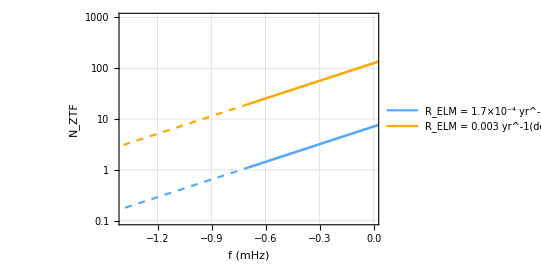

```mathematica
Show[p1,p2,p3]
```

## References

Burdge, K. B., Prince, T. A., Fuller, J., et al. 2020, ApJ,905, 32

Brown, W. R., Kilic, M., Hermes, J. J., et al. 2011, ApJL, 737, L23

Brown, W. R., Kilic, M., Kenyon, S. J., & Gianninas, A. 2016, ApJ, 824, 46

Kilic, M., Brown, W. R., Heinke, C. O., et al. 2016, MNRAS, 460, 4176

Kupfer & Korol, Littenberg, T. B., Shah, S., et al. 2024, ApJ, 963, 100,